# Hydorlogical System Project I Troy Edwards & Baoxiang Pan

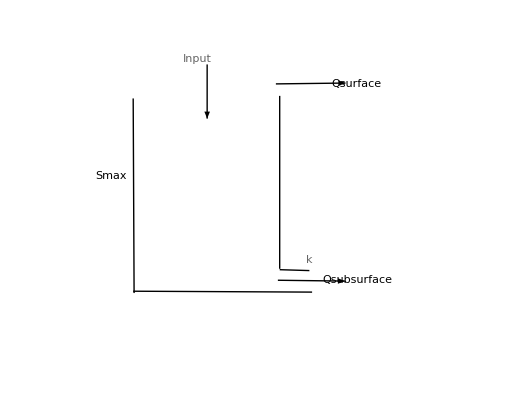
### Model Description -Graphics-

The bucket model works in the following way:
	(1) If the state variable  (S) is less than Smax, the output is a linear response of the state, with the linear factor being k.
	(2) If the state variable (S) is larger than Smax, the output is composes of two parts, the excess part (S-Smax) and the linear response (k*Smax).
The implementation of the model using mathematica language is shown as follows.

```mathematica
Simulation[input_,state_,Smax_,k_]:=Module[{noutput,nstate},
    noutput=If[input+state>Smax,input+state-Smax+k*Smax+state,k*(input+state)];
	nstate=input+state-noutput;
	Return[{noutput,nstate}]];
SequentialSimulation[Input_,Smax_,k_]:=Module[{s0=30,Input2State},
Input2State[{output_,state_},input_]:=Module[{noutput,nstate},
    noutput=If[input+state>Smax,input+state-Smax+k*Smax+state,k*(input+state)];
	nstate=input+state-noutput;
	Return[{noutput,nstate}]];
	FoldList[Input2State,{k*s0,s0},Input]];
```

### Evaluate Criterion: Square Error / Absolute Error

The evaluation criteria is L2 Norm and L1 Norm. The simulation results are all compared with the result when settint Smax at 120 and k at 0.3.

```mathematica
SquareError[simu_,obser_]:=Norm[Map[First,simu-obser]];
AbsoluteError[simu_,obser_]:=Norm[Map[First,simu-obser],1];
ResponseSurface[inputt_,evaluatet_]:=Module[{simu,obser,input,Smax=120,k=0.3},
  input=SequentialInputGeneration[inputt];
  obser=SequentialSimulation[input,Smax,k];
  simu[Smax_,k_]:=SequentialSimulation[input,Smax,k];
  Return[Flatten[Table[{i,j,If[evaluatet==2,SquareError[simu[j,i],obser],AbsoluteError[simu[j,i],obser]]},{i,0.1,0.99,0.01},{j,60,180,3}],1]]];
```

### Scenario Analysis

```mathematica
Scenario Generator
```

This part generate the response surface of the bucket model given different kinds of inputs.

```mathematica
SequentialInputGeneration[i_]:=Module[{InputGeneration,s0=30,Smax=120,k=0.3,n=1000},
	InputGeneration[{input_,state_}]:=Module[{ninput,noutput,nstate},
		{noutput,nstate}=Simulation[input,state,Smax,k];
		ninput=If[i==1,RandomReal[{0,Smax-nstate}],
									              If[i==2,RandomReal[{Smax-nstate,(1+RandomReal[])*(Smax-nstate)}],
		            If[i==3,If[RandomReal[]<0.95,RandomReal[{0,Smax-nstate}],
			                     RandomReal[{Smax-nstate,(1+RandomReal[])*(Smax-nstate)}]],
			           If[RandomReal[]>0.5,RandomReal[{0,Smax-nstate}],
				          RandomReal[{Smax-nstate,(1+RandomReal[])*(Smax-nstate)}]]]]];
		Return[{ninput,nstate}]];
	Return[Map[First,NestList[InputGeneration,{0,s0},n]]]];
```

```mathematica
Scenario I:  state<Smax
```

In the firs scenario, the input is generated constrained by the condition that the state is always less than Smax.

```mathematica
response11=ResponseSurface[1,1];
response12=ResponseSurface[1,2];
```

Response Surface of N1 Norm

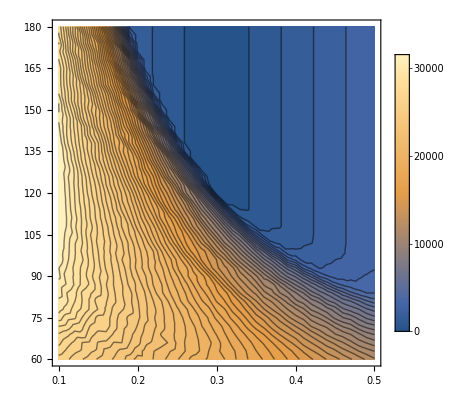

```mathematica
ListContourPlot[response11,Contours->50,PlotLegends->Automatic]
```

Response Surface of N2 Norm

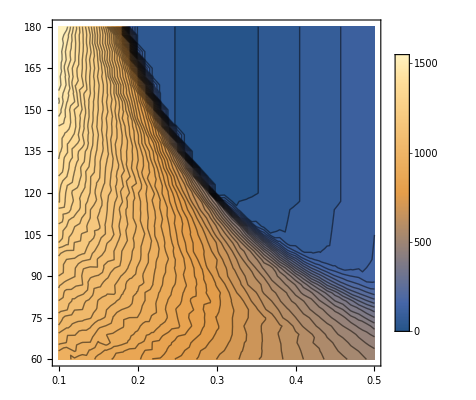

```mathematica
ListContourPlot[response12,Contours->50,PlotLegends->Automatic]
```

The best parameter sets are is the higher frequency electromagnetic color region, which is very widely spreaded in both evaluating criteria. Smax is more spreaded than k, this is for the reason that in this scenario, Smax takes little or no effect.

```mathematica
Scenario II:  state>Cmax
```

In the second scenario, the input is generated constrained by the condition that the state is always larger than Smax.

```mathematica
response21=ResponseSurface[2,1];
response22=ResponseSurface[2,2];
```

Response Surface of N1 Norm

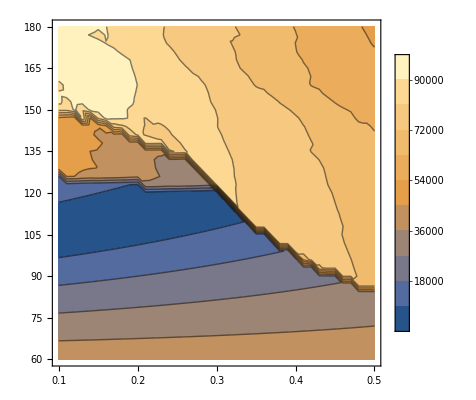

```mathematica
ListContourPlot[response21,Contours->10,PlotLegends->Automatic]
```

Response Surface of N2 Norm

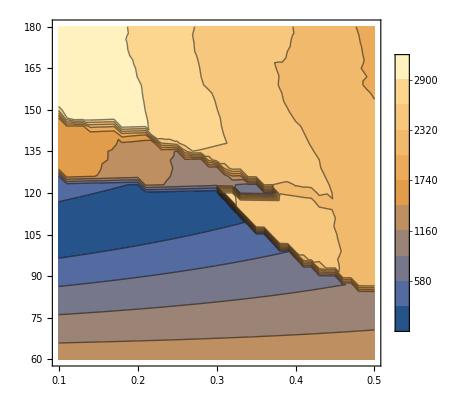

```mathematica
ListContourPlot[response22,Contours->10,PlotLegends->Automatic]
```

The best parameter sets are is the higher frequency electromagnetic color region, which is  widely spreaded in both evaluating criteria. Smax is less spreaded than k. this is for the reason that in this scenario, Smax always takes  effects.

```mathematica
Scenario III:  If[t<t*,state<Cmax, state>Cmax]
```

In the third scenario, the input is generated constrained by the condition that in the firs half temporal period, the state is always smaller than Smax while in the latter period, it is always larger than Smax.

```mathematica
response31=ResponseSurface[3,1];
response32=ResponseSurface[3,2];
```

Response Surface of N1 Norm

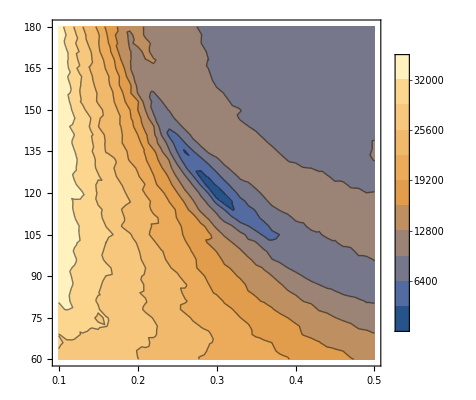

```mathematica
ListContourPlot[response31,Contours->10,PlotLegends->Automatic]
```

Response Surface of N2 Norm

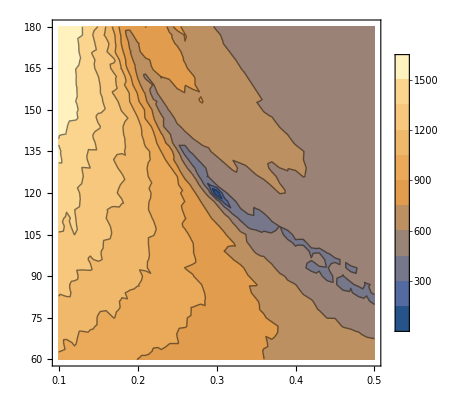

```mathematica
ListContourPlot[response32,Contours->10,PlotLegends->Automatic]
```

The best parameter sets are is the higher frequency electromagnetic color region, which is less spreaded in both evaluating criteria than the above two scenarios. This is for the reason that in this scenario, both Smax and k are taking effects in shaping the outputs. The output can vice versa determine the parameters.

```mathematica
Scenario IV:  state<Cmax || state>Cmax
```

In the fourth scenario, the input is generated constrained by the condition that the state is permutating around  Smax.

```mathematica
response41=ResponseSurface[4,1];
response42=ResponseSurface[4,2];
```

Response Surface of N1 Norm

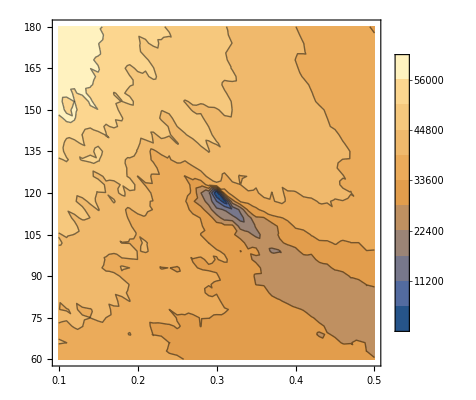

```mathematica
ListContourPlot[response41,Contours->10,PlotLegends->Automatic]
```

Response Surface of N2 Norm

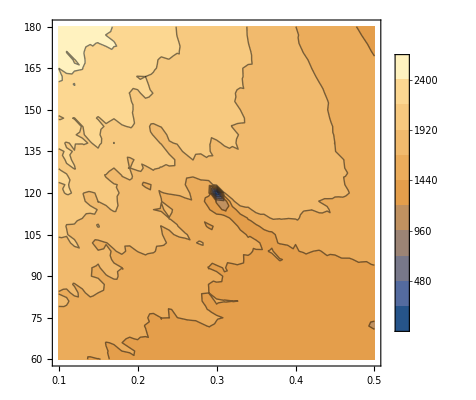

```mathematica
ListContourPlot[response42,Contours->10,PlotLegends->Automatic]
```

The best parameter sets are is the higher frequency electromagnetic color region, which is very concentrated in both evaluating criteria. This is for the reason that in this scenario, the input-output relationship represents the whole mechanism of the model, which can cast a precise calibration of the results.